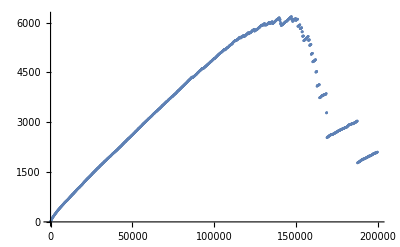

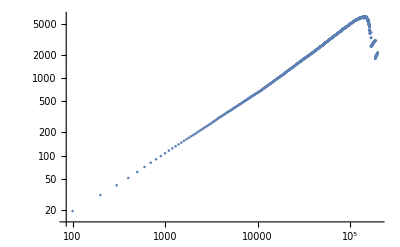

```mathematica
s="D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\D_L500OT200000_u60t100.txt";
data=ReadList[s,{Number,Number}];
ListPlot[data];
datar=Table[{i,Mean[Cases[data,{i,_}]][[2]]},{i,0,Max[data],100}];
ListPlot[datar]
ListPlot[datar,ScalingFunctions->{"Log","Log"}]
```

-0.458316+0.736999 x

-1.77553+0.892314 x

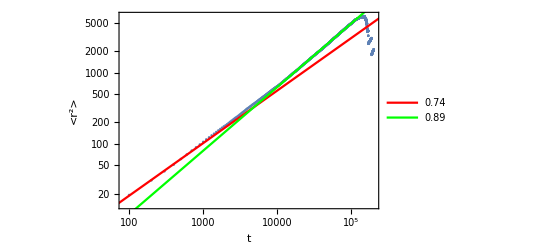

-0.957825+0.798092 Log[x]

```mathematica
fitdata=Take[datar,{2,8}];
f=Fit[Log@fitdata,{1,x},x]
fitdata=Take[datar,{100,1000}];
g=Fit[Log@fitdata,{1,x},x]
Show[ListPlot[datar,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{Style["t",24],Style["<r^2>",24]}],Plot[{f,g},{x,0,1000000},PlotStyle->{Red,Green},PlotLegends->{"0.74","0.89"}]]
```